```mathematica
Clear["Global`*"]
```

# Differential equations

## Data:

Solve the diff eqn:

```mathematica
eqn=-u''[x]==1+x;
```

object to the boundary conditions:

```mathematica
bnd1=u[0]==0;
```

and

```mathematica
bnd2=u[1]==0;
```

## Solution:

Solve the eqn, object to the boundary conditions:

```mathematica
sln = DSolve[{eqn,bnd1,bnd2},u[x],x]
```

{{u[x]→1/6 (4 x-3 x^2-x^3)}}

Extract u[x] from the first element of the list sln and assign it to the function u:

```mathematica
u[x_]=u[x]/.sln[[1]]//FullSimplify
```

-1/6 (-1+x) x (4+x)

Verify that u(x) is indeed a solution:

```mathematica
eqn//FullSimplify
```

True

Verify that boundary conditions are satisfied:

```mathematica
bnd1//FullSimplify
```

True

```mathematica
bnd2//FullSimplify
```

True

Find the roots of u(x):

```mathematica
Roots[u[x]==0, x]
```

x==1||x==0||x==-4

Plot the solution:

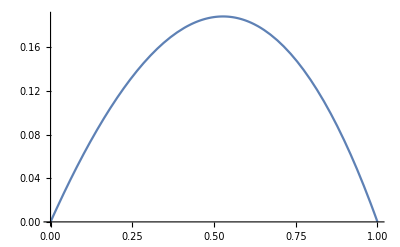

```mathematica
Plot[u[x],{x,0,1}]
```

End.